# Chapter 1 Introduction to Experimental Data Analyst

Experimental Data Analyst (EDA) is a collection of tools and tutorials designed specifically for the needs of physical scientists, engineers, and students of science and engineering. Included are over 30 functions, tutorials in using the functions, tutorials in using Mathematica built-in commands and standard Mathematica packages, and discussions of the underlying theory of data analysis at a variety of levels from beginning undergraduate to practicing researcher. The tutorials make use of a variety of real experimental data drawn from many different fields, and the data is also included in the package.

The material is divided into eight chapters, beginning with this chapter, which provides an overview of the contents. The chapters can be accessed as a hard-copy version or read online as Mathematica notebooks. The notebooks can be read with the front end included with Mathematica or with the free MathReader program available from www.wolfram.com/products/mathreader; in the former case, the notebooks can be interactive, and the reader is encouraged to experiment with the commands and supplied data sets.

The chapters do not all have to be read in order. In general, we recommend that you look over this chapter in its entirety before going on to the others. Section 1.1.1 gives further recommendations of which chapters and sections are probably prerequisites for succeeding ones.

## 1.1 Summary and Use of EDA

### 1.1.1 Summary of the Chapters of EDA

Chapter 2 deals with methods of getting data into Mathematica so that it may be analyzed. This chapter is independent of all other chapters included with EDA. It discusses techniques to read and write files containing data sets and also introduces the EDA programs ImportData and ExportData.

Chapter 3 discusses a topic which pervades data analysis in the physical sciences and engineering: error analysis. Here a tutorial is supplied. Although the level is suitable for an undergraduate student in the sciences, we are also aware of many professional researchers whose education and training have managed to miss some of the material discussed here. In addition, EDA supplies programs and constructs to simplify error analysis, and they are introduced in this chapter. The EDA functions discussed are AdjustSignificantFigures, CombineWithError, DivideWithError, PlusWithError, PowerWithError, Quadrature, SubtractWithError, and TimesWithError. Also, EDA defines Data and Datum constructs for doing propagation of errors; these constructs are introduced in this chapter. The functions and constructs discussed here are used in later chapters.

Chapters 4 through 8 are the “heart” of the analysis tools provided by EDA.

Chapter 4 introduces one of the most commonly performed tasks in data analysis: fitting data to linear models, especially straight lines and curves. Section 4.1 provides background discussions of a linear fit, least-squares techniques, evaluation of the quality of the fit, etc.; some familiarity with this material is assumed in all later sections. The remainder of Chapter 4 discusses the EDA function LinearFit, which performs linear least-squares fits to data. Included is a discussion of the related EDA functions ShowLinearFit and ToLinearFunction. The LinearFit function is used in all subsequent chapters. Also, many other EDA functions have similar syntax. Thus, some familiarity with its syntax and options is recommended.

Chapter 5 extends the materials of Chapter 4 to arbitrary models. It introduces the EDA function EDAFindFit and the related functions ShowFitFunction and ToFitFunction. Also discussed are some convenience functions that define peak shapes; these are BreitWigner, Galatry, Gaussian, Lorentzian, PearsonVII, RelativisticBrietWigner, and Voigt. Most of the information in this chapter is not used in later discussions, although the FindPeaks function discussed in Chapter 8 is primarily intended as a companion to EDAFindFit.

Chapter 6 discusses techniques to eliminate noise in data and to fill in missing values. It also discusses the related topic of fitting data when a model is not available or appropriate. The chapter introduces the EDA functions SmoothData, LoessFit, and FillData. There is also a tutorial on using built-in Mathematica functions to smooth data, and the algorithm used by the FindPeaks program discussed in Chapter 8 is introduced here. With the exception of the algorithm of FindPeaks, nothing in later chapters depends on anything appearing here.

Chapter 7 discusses techniques to fit data to lines and curves when one or more of the data points may be “wild”, that is the data contains “outliers.”  Alternatives to least-squares techniques should be considered in this case since an outlier can have a significant effect on the least-squares fit. The chapter introduces the EDA functions RobustCurveFit and RobustLineFit. Nothing in the chapter is required for Chapter 8.

Chapter 8 discusses what to do when the relations in a data set are not known. Graphical techniques are explored in Section 8.1. The discussion includes the EDA function EDAListPlot, which is briefly introduced in Section 1.3,  the EDA function  BoxPlot is also discussed. Section 8.2 is a tutorial on using Mathematica built-in functions to transform the data; the discussion is one of the more advanced in EDA. Nonetheless, Section 8.2 only “scratches the surface” of this topic. Finally, Section 8.3 gives a full discussion of the FindPeaks function; this function was briefly introduced in Chapter 5, and its algorithm is discussed in Section 6.1.5.

### 1.1.2 Using EDA

Although EDA notebooks include general purpose tutorials, EDA is also a collection of software tools, and this subsection discusses using the software. The software consists of 12 Mathematica packages, written in the Mathematica language, that define EDA's functions, options, etc.

The easiest way to access an EDA function is to execute the following.

```mathematica
Needs["EDA`"]
```

If the command is executed and produces error messages, you should consult your installation document for the package.

Once EDA has successfully loaded, you can use Mathematica just as if all the packages of EDA were loaded, except for a two differences.

First, since all of the packages are loaded only when needed, the size of the Mathematica kernel is over a megabyte smaller than if they were actually loaded.

Second, the first time you invoke an EDA function, the package containing the function has to be loaded. Often, other packages are used by the package containing the definition of the function you have invoked and they must be loaded, too. For example, the package containing the definition of LinearFit loads six other packages; some of these load yet other packages. For this example, invoking LinearFit loads 10 other packages besides the one containing the definition for LinearFit itself. Therefore, the first time you invoke some EDA functions, it may take a few moments before everything is loaded and the program begins its work. Second and subsequent invocations will begin working almost immediately.

## 1.2 The EDA Data Format

The EDA programs expect the data to be in a particular format, and confusing and nonsensical results can occur by not using this standard format.

The “dependent” variable is usually graphed on the vertical or y axis, while the “independent” variable is usually graphed on the horizontal or x axis.

If the data contains values only of the dependent variable, then the format must be a list.

{y1,y2,...,yN}

Here y1 is the value of the first data point, y2 the second, and yN the Nth data point. The notation used implies that there are exactly N data points in the data set. EDA will assume that the corresponding values of the independent variable are just the integers from 1 through N.

{1,2,...,N}

If the data contain values for both the independent and dependent variables, then the format is in x, y pairs.

{ {x1,y1},{x2,y2},...,{xN,yN} }

Here xi is the value of the ith independent variable and yi the value of the ith dependent variable.

If there is an experimental error associated with one of the variables in the data set, by definition that variable is the dependent one.

{ {x1,{y1,erry1}},{x2,{y2,erry2}},...,{xN,{yN,erryN}} }

Here erryi is the experimental error in the yi value.

Note that if there are errors associated with the dependent variable, then the values of the independent variable must be explicitly given in the data set.

{ {y1,erry1},{y2,erry2},...,{yN,erryN} } (*WRONG!*)

The above list is wrong because its format is identical with the list that specifies only independent-dependent variable pairs.

If there are experimental errors associated with both variables, the format contains both errors.

{ {{x1,errx1},{y1,erry1}},{{x2,errx2},{y2,erry2}},...,{{xN,errxN},{yN,erryN}} }

In this example, errxi is the experimental error in the xi value. Note that in this case the distinction between the independent and dependent variables is somewhat arbitrary. Often the choice is made by the experimenter on a case by case basis.

Once the data is in this standard EDA format, all software programs supplied by the package can make automatic choices about which coordinates have associated errors. This ability is crucial in order for many of the package functions to return reasonable results.

EDA provides utilities for describing a data set that is in this standard format; these utilities are described in the next section. Here we briefly point out techniques used to put data into this format.

Sometimes the values of the independent and dependent variables are in separate lists.

```mathematica
xvalues={x1,x2,x3,x4,x5,x6};yvalues={y1,y2,y3,y4,y5,y6};
```

Here we designate the xvalues as the independent variables and the yvalues as the dependent ones. Then we can form a data set using Transpose.

```mathematica
mydata2=Transpose[{xvalues,yvalues}]
```

{{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5},{x6,y6}}

The “2” in mydata2 is a mnemonic signaling that there are two variables in the data set, in this case x and y. Thus, a data set of only one variable, the y coordinate, can be called mydata1.

```mathematica
mydata1=yvalues
```

{y1,y2,y3,y4,y5,y6}

These mnemonics are for our convenience; EDA does not pay attention to any such naming conventions.

Suppose there are errors associated with the yvalues in a variable erryvalues.

```mathematica
erryvalues={erry1,erry2,erry3,erry4,erry5,erry6};
```

Then the {yvalue, erryvalue} pairs are formed using Transpose.

```mathematica
Transpose[{yvalues,erryvalues}]
```

{{y1,erry1},{y2,erry2},{y3,erry3},{y4,erry4},{y5,erry5},{y6,erry6}}

Thus, an EDA-consistent data set is formed by combining the terms.

```mathematica
mydata3=Transpose[{xvalues,Transpose[{yvalues,erryvalues}]}]
```

{{x1,{y1,erry1}},{x2,{y2,erry2}},{x3,{y3,erry3}},{x4,{y4,erry4}},{x5,{y5,erry5}},{x6,{y6,erry6}}}

Suppose that in addition to explicit errors in the dependent variable, there are errors associated with the independent variable.

```mathematica
errxvalues={errx1,errx2,errx3,errx4,errx5,errx6};
```

Then we can form {xvalue, errxvalue} pairs.

```mathematica
Transpose[{xvalues,errxvalues}]
```

{{x1,errx1},{x2,errx2},{x3,errx3},{x4,errx4},{x5,errx5},{x6,errx6}}

Finally, we can form an EDA data set with errors in both coordinates.

```mathematica
mydata4=Transpose[{Transpose[{xvalues,errxvalues}],Transpose[{yvalues,erryvalues}]}]
```

{{{x1,errx1},{y1,erry1}},{{x2,errx2},{y2,erry2}},{{x3,errx3},{y3,erry3}},{{x4,errx4},{y4,erry4}},{{x5,errx5},{y5,erry5}},{{x6,errx6},{y6,erry6}}}

## 1.3 EDA Utilities and Supplied Data Sets

EDA supplies some general-purpose utilities, which are described here. This section also discusses the sets of real data supplied with the package.

First we load EDA.

```mathematica
Needs["EDA`"]
```

In the previous section, we defined the following four data sets. We re-define them here.

```mathematica
xvalues={x1,x2,x3,x4,x5,x6};yvalues={y1,y2,y3,y4,y5,y6};
```

```mathematica
mydata2=Transpose[{xvalues,yvalues}]
```

{{x1,y1},{x2,y2},{x3,y3},{x4,y4},{x5,y5},{x6,y6}}

```mathematica
mydata1=yvalues
```

{y1,y2,y3,y4,y5,y6}

```mathematica
erryvalues={erry1,erry2,erry3,erry4,erry5,erry6};
```

```mathematica
mydata3=Transpose[{xvalues,Transpose[{yvalues,erryvalues}]}]
```

{{x1,{y1,erry1}},{x2,{y2,erry2}},{x3,{y3,erry3}},{x4,{y4,erry4}},{x5,{y5,erry5}},{x6,{y6,erry6}}}

```mathematica
errxvalues={errx1,errx2,errx3,errx4,errx5,errx6};
```

```mathematica
mydata4=Transpose[{Transpose[{xvalues,errxvalues}],Transpose[{yvalues,erryvalues}]}]
```

{{{x1,errx1},{y1,erry1}},{{x2,errx2},{y2,erry2}},{{x3,errx3},{y3,erry3}},{{x4,errx4},{y4,erry4}},{{x5,errx5},{y5,erry5}},{{x6,errx6},{y6,erry6}}}

The number at the end of each name is the number of variables in the data set.

The utility DataParameters returns the number of data points and the number of variables in a data set.

```mathematica
?DataParameters
```

DataParameters[data] determines the number of data points, npoints,
	and number of variables, nvars, in data and returns {npoints,nvars}.
	The data is assumed to be in the format of Experimental Data
	Analyst.

```mathematica
DataParameters[mydata1]
```

{6,1}

```mathematica
DataParameters[mydata2]
```

{6,2}

```mathematica
DataParameters[mydata3]
```

{6,3}

```mathematica
DataParameters[mydata4]
```

{6,4}

The utility UnpackData provides this information plus separate lists for the variables.

```mathematica
?UnpackData
```

UnpackData[data] takes data formatted in the EDA standard
	and returns {npoints, nvars, x, errx, y, erry} in that order, where
	`npoints' is the number of data points, `nvars' the number of
	variables, `x' the independent variable, `errx' the error in `x',
	`y' the dependent variable, and `erry' the error in `y'. If `nvars'
	is 1, the `x' returned is {1, 2, ... , npoints}. If no errors appear
	in the data, the error variables are filled in with a list of 1s whose
	length is equal to `npoints'. In all cases, the data is returned sorted
	by the value of the independent variable.

```mathematica
UnpackData[mydata1]
```

{6,1,{1.,2.,3.,4.,5.,6.},{1,1,1,1,1,1},{y1,y2,y3,y4,y5,y6},{1,1,1,1,1,1}}

Note that the program has generated the values of the independent variable, {1., 2., ... , 6.}, and has returned all 1s as the errors in dependent and independent variables. We now unpack the other three data sets.

```mathematica
UnpackData[mydata2]
```

{6,2,{x1,x2,x3,x4,x5,x6},{1,1,1,1,1,1},{y1,y2,y3,y4,y5,y6},{1,1,1,1,1,1}}

This time the values for the independent variable are extracted from the data set.

```mathematica
UnpackData[mydata3]
```

{6,3,{x1,x2,x3,x4,x5,x6},{1,1,1,1,1,1},{y1,y2,y3,y4,y5,y6},{erry1,erry2,erry3,erry4,erry5,erry6}}

This adds the error in the dependent variable to the extracted lists.

```mathematica
UnpackData[mydata4]
```

{6,4,{x1,x2,x3,x4,x5,x6},{errx1,errx2,errx3,errx4,errx5,errx6},{y1,y2,y3,y4,y5,y6},{erry1,erry2,erry3,erry4,erry5,erry6}}

Now all the “slots” returned by UnpackData have been filled with the actual data.

The built-in Mathematica function ListPlot is convenient for displaying data sets of one or two variables. EDA supplies a generalized version, EDAListPlot, that recognizes the EDA data format and automatically displays error bars when the data contain experimental errors. We then generate four data sets of numbers and illustrate the following (note that we "recycle" the names mydata1, mydata2, mydata3, and mydata4).

```mathematica
mydata1=Table[Prime[x],{x,5}]
```

{2,3,5,7,11}

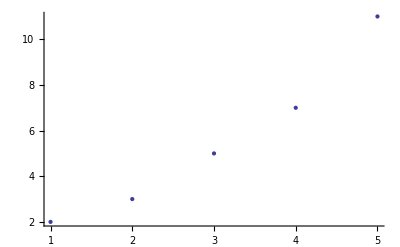

```mathematica
EDAListPlot[mydata1]
```

```mathematica
mydata2=Table[{x^2,Prime[x]},{x,5}]
```

{{1,2},{4,3},{9,5},{16,7},{25,11}}

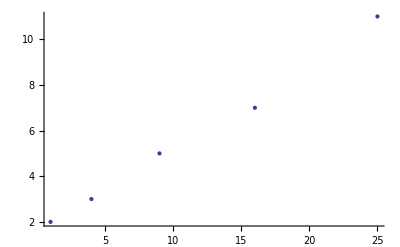

```mathematica
EDAListPlot[mydata2]
```

```mathematica
mydata3=N[Table[{x^2,{Prime[x],√x}},{x,5}]]
```

{{1.,{2.,1.}},{4.,{3.,1.41421}},{9.,{5.,1.73205}},{16.,{7.,2.}},{25.,{11.,2.23607}}}

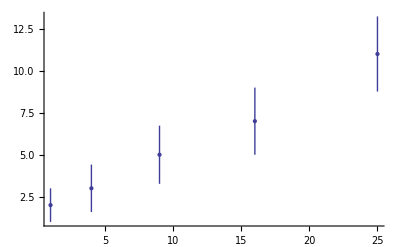

```mathematica
EDAListPlot[mydata3]
```

```mathematica
mydata4=N[Table[{{x^2,x},{Prime[x],√x}},{x,5}]]
```

{{{1.,1.},{2.,1.}},{{4.,2.},{3.,1.41421}},{{9.,3.},{5.,1.73205}},{{16.,4.},{7.,2.}},{{25.,5.},{11.,2.23607}}}

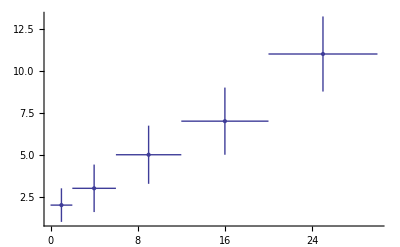

```mathematica
EDAListPlot[mydata4]
```

EDAListPlot has many more capabilities than those illustrated here and the full discussion of this function is found in Section 8.1.1.

As already mentioned, EDA supplies a collection of real experimental data drawn from a variety of fields of science. They are used for illustration and are located in the EDA`Data` directory, which also contains a file named Index.txt that correlates the data files with the notebooks that discuss them.

All of the data files are Mathematica packages with the exception of Aptec.txt and Cs137.dat, which are an ASCII data dump and a binary data file, respectively.

For the data files that are Mathematica packages, the data may be loaded with the EDA function LoadData.

```mathematica
?LoadData
```

LoadData[label] loads an EDA data set identified by label. If
	the EDAShowProgress option is set to True (the default), the actual
	name(s) of the data set(s) being loaded are given as a Message,
	otherwise they are not. In many cases, but not all, the name of
	the data set is the same as label, except that the name of the data
	set has the string "Data" appended. LoadData[], i.e., no input
	argument, lists the legal values for label.

As indicated in the usage message, we can get a list of valid arguments to the program by calling it with no arguments.

```mathematica
LoadData[]
```

LoadData::contents: The names that are valid arguments to LoadData are: AbsoluteZero
Anscombe
Boyle
Chwirut
CThDating
Cobalt60
Darwin
FreeFall
Ganglion
Interneuron
KPiPi
MassSpec
MassSpec2
Ozone
PearsonYork
Population
EDAReactance
Siegel
Thermocouple
Wampler

As also indicated in its usage message, LoadData has an option to control its behavior. Some functions, such as UnpackData, do not have options.

```mathematica
Options[UnpackData]
```

{}

Other functions have many options.

```mathematica
TableForm[Options[EDAListPlot]]
```

AlignmentPoint→Center
AspectRatio→1/GoldenRatio
Axes→True
AxesLabel→None
AxesOrigin→Automatic
AxesStyle→{}
Background→None
BaselinePosition→Automatic
BaseStyle→{}
ClippingStyle→None
ColorFunction→Automatic
ColorFunctionScaling→True
ColorOutput→Automatic
ContentSelectable→Automatic
DataRange→Automatic
Epilog→{}
ErrorBarFunction→Automatic
Filling→None
FillingStyle→Automatic
Frame→False
FrameLabel→None
FrameStyle→{}
FrameTicks→Automatic
FrameTicksStyle→{}
GridLines→None
GridLinesStyle→{}
ImageMargins→0.
ImagePadding→All
ImageSize→Automatic
InterpolationOrder→None
Joined→False
Joined→True
LabelStyle→{}
MaxPlotPoints→∞
Mesh→None
MeshFunctions→{#1&}
MeshShading→None
MeshStyle→Automatic
Method→Automatic
PlotLabel→None
PlotMarkers→None
PlotRange→Automatic
PlotRangeClipping→True
PlotRangePadding→Automatic
PlotRegion→Automatic
PlotStyle→Automatic
PreserveImageOptions→Automatic
Prolog→{}
RotateLabel→True
Ticks→Automatic
TicksStyle→{}
DisplayFunction:>$DisplayFunction
FormatType:>TraditionalForm
PerformanceGoal:>$PerformanceGoal

LoadData has a single option.

```mathematica
Options[LoadData]
```

{EDAShowProgress→True}

The option has its own usage message.

```mathematica
?EDAShowProgress
```

EDAShowProgress is an option for various routines. When set to True, the
	routine will print messages showing its progress in performing
	its tasks. If set to False, no such information is printed.

As indicated, by default LoadData names the data set(s) it is loading.

```mathematica
LoadData[Boyle]
```

LoadData::name: Loading: BoyleData

The option can stop the naming of the data set.

```mathematica
LoadData[Boyle,EDAShowProgress->False]
```

Note that in all programs in Mathematica, options must be given last.

The names of the data sets, such as BoyleData, are known to the Mathematica kernel through the initialization of EDA. As discussed in Section 1.1.2, this means that you can load the data just by naming it; you may append a semicolon to the command to keep the data from being printed on your screen. You can also cause a data set to load by naming the data set in a call to a program.

```mathematica
DataParameters[GanglionData]
```

{14,2}

You may prefer to use LoadData, however, because it provides error checking.

```mathematica
LoadData[noSuchData]
```

LoadData::noname: Name noSuchData is not known.  LoadData[] will list all known names.

$Failed

### 1.3.1 Contents of the EDA`Data` Directory

This listing does not include the files Aptec.txt or Cs137.dat, an ASCII data file and a binary data file, respectively.

```mathematica
LoadData[AbsoluteZero]
```

LoadData::name: Loading: AbsoluteZeroData

```mathematica
?AbsoluteZeroData
```

AbsoluteZeroData is student-collected data on the pressure and
	temperature of a fixed volume of gas, reported in John R.
	Taylor, "An Introduction to Error Analysis: The Study of
	Uncertainties in Physical Measurements" (University Science
	Books, Mill Valley California, 1982), pg 160. The format
	of each data point is {p, t}, where 'p' is the pressure in
	mm of mercury and 't' the temperature in degrees Centigrade.
	The student judged that his measurements of p had neglible
	uncertainty and those of t were all equally uncertain, with
	an uncertainty of "a few degrees".

```mathematica
LoadData[Anscombe]
```

LoadData::name: Loading: AnscombeData[[i]], for i = 1,2,3,4

```mathematica
? AnscombeData
```

AnscombeData is a quartet of made-up data devised by F.J.
	Anscombe, American Statistician 27 (Feb. 1973), pg 17.
	All four data sets, AnscombeData[[1]], AnscombeData[[2]],
	AnscombeData[[3]], and AnscombeData[[4]], have almost identical
	averages and fit to almost identical straight lines. The format
	of each data set is {x, y}, where neither coordinate has units.

```mathematica
LoadData[Boyle]
```

LoadData::name: Loading: BoyleData

```mathematica
? BoyleData
```

BoyleData is based on data for testing Boyle's law taken by a 
	first-year student at the University of Toronto in the Department of
	Physics undergraduate laboratories in 1983. A fixed quantity of dry air
	at room temperature had its pressure and volume measured for a
	number of different values of the pressure. The format of each
	data point is { {p, errp}, {v, errv} }, where p and errp are
	the value and error in the pressure, measured in cm of Hg, and v
	and errv are the value and error in the volume, measured in cm^3.

```mathematica
LoadData[Chwirut]
```

LoadData::name: Loading: ChwirutData

```mathematica
?ChwirutData
```

ChwirutData is data on ultrasonic calibration, taken by Daniel Chwirut
	in the 1970s at the National Institutes of Standards and
	Technology (NIST) in the U.S.A. The data format is {d, r}, where d
	is the metal distance and r is the ultrasonic response. The dataset
	is now part of the Statistical Reference Datasets (StRD) maintained
	by NIST at www.nist.gov/itl/div898/strd, where it is identified
	as "chwirut2."

```mathematica
LoadData[CThDating]
```

LoadData::name: Loading: CThDatingData

```mathematica
? CThDatingData
```

CThDatingData compares the dating of samples of coral using two
	different techniques: carbon-14 and thorium.  It can be viewed
	as a calibration of carbon-14 dating.  The data is from Edouard Bard,
	Bruno Hamelin, Richard G. Fairbanks, and Alan Zindler, Nature 345,
	(May, 1990), pg 405. The format of the data is {C14 age,
	{thorium age minus C14 age, error in thorium age minus C14 age}}, where
	all numbers are in years before the present. The errors are one standard
	deviation, not the two standard deviation errors given in the original
	source.

```mathematica
LoadData[Cobalt60]
```

LoadData::name: Loading: Cobalt60Data

```mathematica
? Cobalt60Data
```

Cobalt60Data is part of a cobalt-60 nuclear spectrum. The
	format is: {channel, counts}. The data was collected in the second-year
	Lab of the Department of Physics, University of Toronto with a NaI 
	scintillator and a PC-based multichannel analyzer running PC-MCA software 
	by David Harrison (1990, unpublished).

```mathematica
LoadData[Darwin]
```

LoadData::name: Loading: CrossFertilizedData
and SelfFertilizedData

```mathematica
?CrossFertilizedData
```

CrossFertilizedData is the height of 15 Zea Mays plants that were
	cross-fertilized, measured in inches. The data was taken by Darwin
	in 1878.

```mathematica
?SelfFertilizedData
```

SelFertilizedData is the height of 15 Zea Mays plants that were
	self-fertilized, measured in inches. The data was taken by Darwin
	in 1878.

```mathematica
LoadData[FreeFall]
```

LoadData::name: Loading: FreeFallData

```mathematica
?FreeFallData
```

FreeFallData is free-fall data taken by Professor A.W. Key,
	Department of Physics, University of Toronto using an apparatus from the
	undergraduate laboratory (1994, unpublished).  The dropped
	object was a round plastic ball.  The data format is
	{ {t, errt}, {s, errs}}, where t is the time, errt is the
	error in the time, both in ms, s is the distance, and errs is the
	error in the distance, both in meters.

So far, we have loaded the data sets and then used ? to display information on the data.  For the remainder of this section, we use the fact that ? will load the data automatically, as discussed in Section 1.1.2. The symbol ? is shorthand for NullInformation[ ..., LongForm → False].

```mathematica
?GanglionData
```

GanglionData is data for the ratio of the central ganglion cell density
	to the peripheral density versus retinal area for 14 cat fetuses.
	The fetuses ranged in age from 35 to 62 days, and the retinal area
	is approximately monotonic in the age of the fetus. The data is from
	Barry Lia, Robert W. Williams, and Leo M Chalupa, Science 236, (1987)
	pg 848. The format of the data is {area, CP}, where area is in mm^2
	and CP is dimensionless.

```mathematica
?InterneuronData
```

InterneuronData is data of oscillations of interneuron networks
	driven by metabotopic glutamate receptor activation in slices of
	rat hippocampus and neocortex. The data is from Miles A.
	Whittington, Roger D. Traub, and John G.R. Jefferys, Nature 373,
	(1995) pg 612. The format of the data is {ipscTau, frequency}, where
	'ipscTau' is the decay constant of the inhibitory postsynaptic currents
	in ms and 'frequency' is the oscillation frequency of the network
	in Hz.

```mathematica
?KPiPiData
```

KPiPiData is data on the decay of the K*(1780) into (K0, Pi+, Pi-).
	The format of each data point is { M(K0, Pi-)^2, M(Pi+, Pi-)^2 },
	where M is the invariant mass in Gev/c^2. The data was collected by
	D. Aston et al. at the Stanford Linear Accelerator in 1986
	(SLAC-REP-298, May 1986), using an 11 GeV/c K- beam incident on
	liquid hydrogen.

```mathematica
?MassSpecData
```

MassSpecData is mass spectrometer data for two isotopes,
	taken by Dr. Alex Young, Dept. of Chemistry, Univ. of Toronto
	(1995, unpublished). The format is {amu,ions}, where amu
	is the mass, in atomic mass units, and ions is the number of
	ions.

```mathematica
?MassSpec2Data
```

MassSpec2Data is ionization data for neon from a mass
	spectrometer. The data was collected by an apparatus in the
	undergraduate laboratories of the Dept. of Physics, Univ.
	of Toronto, during the Winter of 1993, by Mr. Youri Zabbal,
	when he was an undergraduate student. The format is 
	{voltage, current}, where the voltage is in volts and the
	current is in mA.

```mathematica
?OzoneData
```

OzoneData is data on ozone levels in the atmosphere on December 25,
	1988. The data was taken by the Total Ozone Measurement Spectrometer
	(TOMS) aboard the Nimbus 7 satellite. The 60 rows of data correspond
	to latitudes 50 degrees south to 10 degrees north in one degree bins.
	The 60 columns correspond to longitudes of 180 degrees west to 105 degrees
	west in 1.25 degree bins. The units of the data are Dobson units.

```mathematica
?PopulationData
```

PopulationData is the population of the 10 largest cities
	of 16 countries as reported by the 1967 "World Almanac".
	The countries listed are, in order: Sweden, the Netherlands,
	Canada, France, Mexico, Argentina, Spain, England, Italy,
	West Germany, Brazil, the Soviet Union, Japan, the United
	States, India, and China. Populations are in 100,000s. The
	countries are sorted by the value of the median of the population.
	The data for each individual country is available as, for example,
	"SwedenData".

```mathematica
?PearsonYorkData
```

PearsonYorkData is based on a data set of x, y pairs due to K.
	Pearson, Philos, Mag 2, (1901) pg 2. It has been weighted by
	Derek York, Canadian Journal of Physics 44, (1966) pg 1079. The format
	of the data is { {x, errx}, {y, erry} }.

```mathematica
?ReactanceData
```

ReactanceData is data from an LRC circuit being driven by
	an AC voltage (V). The phase shift of the voltage (Vc) across
	the capacitor, with respect to V, is theta, and y = Cot[theta].
	The variable omega is the frequency of the supplied voltage,
	in radians per second. The format of the data is { {omega, erromega},
	{y, erry} }. The data was taken by Jay Orear, American Journal of 
	Physics 50, (1982) pg 912.

```mathematica
?SiegelData
```

SiegelData is a made-up pathological set of data devised by
	Andrew F. Siegel, Biometrika 69, (1982) pg 242. The format
	is {x,y}, where neither coordinate has units.

```mathematica
?ThermocoupleData
```

ThermocoupleData is experimental data of a thermocouple calibration
	given by Philip R. Bevington's "Data Reduction and Error Analysis"
	(McGraw Hill, 1969), pg 138. The format of each data point is
	{T, {V, dV}}, where T is the temperature in degrees Celsius, V the
	voltage in mV, and dV the error in V in mV.

```mathematica
?WamplerData
```

WamplerData is a set of synthetic data devised to test linear
	least-squares fitters. It was devised by R.H. Wampler (1970)
	and is discussed in the Journal of the American Statistical
	Association, 65, pp. 549-565; in that reference it is the fifth
	data set presented. The format of the data is {x, y} pairs.